```mathematica
Multinomial[{1, 2, 3}, {1, 2, 3}, {1, 2, 3}]
```

{6,90,1680}

```mathematica
Expand[(x + y + z) ^6]
```

x^6+6 x^5 y+15 x^4 y^2+20 x^3 y^3+15 x^2 y^4+6 x y^5+y^6+6 x^5 z+30 x^4 y z+60 x^3 y^2 z+60 x^2 y^3 z+30 x y^4 z+6 y^5 z+15 x^4 z^2+60 x^3 y z^2+90 x^2 y^2 z^2+60 x y^3 z^2+15 y^4 z^2+20 x^3 z^3+60 x^2 y z^3+60 x y^2 z^3+20 y^3 z^3+15 x^2 z^4+30 x y z^4+15 y^2 z^4+6 x z^5+6 y z^5+z^6

```mathematica
Exapnd[(x + y + z) ^ 90]
```

Exapnd[(x+y+z)^90]

```mathematica
Exapnd[(x + y + z) ^ 1680]
```

Exapnd[(x+y+z)^1680]

```mathematica
Coefficient[, x + y ^ 2 * z]
```

{0,0,0}

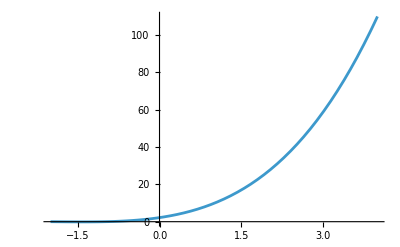

```mathematica
Plot[Multinomial[x, 1 / 2, 3], {x, -2, 4}]
```

```mathematica
ComplexPlot3D[Multinomial[x,1/2],{x,-6 -90 *I,2+1680I},PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
Series[Multinomial[x, 6, 1 / 2], {x, 90, 1680}] // FullSimplify
```

Series[Multinomial[x, 6, 1 / 2], {x, 90, 1680}] // FullSimplify